# Mathematica Help Session #1

## Definition of functions, and how to plot them:

```mathematica
f[x_]:=x^2+5-3x
```

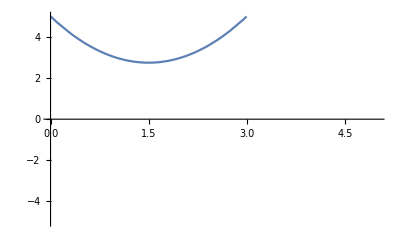

```mathematica
Plot[f[x],{x,-5,5},PlotRange->{{0,5},{-5,5}}]
```

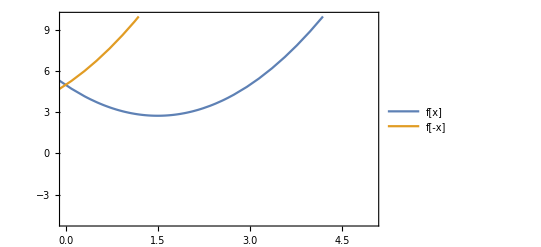

```mathematica
Plot[{f[x],f[-x]},{x,-5,5},PlotRange->{{0,5},{-5,10}},Frame->True,PlotLegends->{"f[x]","f[-x]"}]
```

## Plotting Func vs Data Points

```mathematica
xData={1,2,3,4,5};
yData={0.5,1.2,2.1,3.8,5.0};
(*Create a list of data points using Transpose*)
dataPoints=Transpose[{xData,yData}];
```

```mathematica
data={{1,0.5},{2,1.2},{3,2.1},{4,3.8},{5,5.}};
```

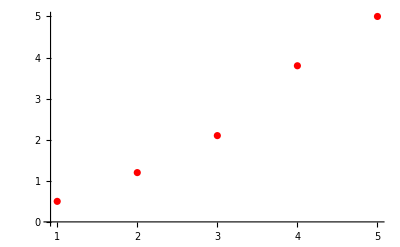

```mathematica
p1=ListPlot[data,PlotStyle->Red]
```

```mathematica
FindFit[data,a x+b,{a,b},x]
```

{a→1.16,b→-0.96}

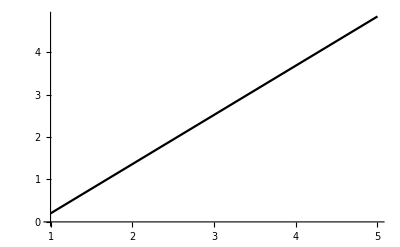

```mathematica
p2=Plot[a x+b/.{a->1.16,b->-0.96},{x,1,5},PlotStyle->Black]
```

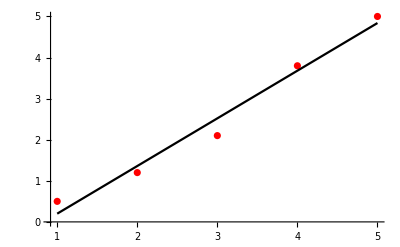

```mathematica
Show[p1,p2]
```

## Differential Eqns

```mathematica
(*Define the differential equation*)
ode:=y''[x]+ω^2 y[x]==0;

(*Symbolically solve the ODE*)
solN=NDSolve[{ode/.ω->1,y[0]==0,y[Pi/2]==1},y[x],{x,0,5}];
sol=DSolve[{ode/.ω->1,y[0]==0,y[Pi/2]==1},y[x],x];
```

```mathematica
(*Display the symbolic solution*)
sol
```

{{C[1] Cos[x]+C[2] Sin[x]→Sin[x]}}

```mathematica
g[x_]:=y[x]/.solN
```

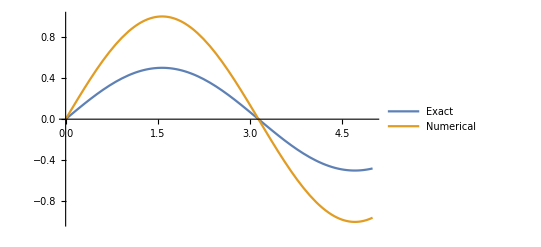

```mathematica
Plot[{0.01+g[x],y[x]/.sol},{x,0,5},PlotLegends->{Exact (Shifted),Numerical}]
```

```mathematica
y[0]==0,y[Pi/2]==1
```

```mathematica
ode
```

-C[1] Cos[x]-C[2] Sin[x]+ω^2 (C[1] Cos[x]+C[2] Sin[x])==0

```mathematica
DSolve[{ode/.ω->1},y[x],x]
```

{{y[x]→C[1] Cos[x]+C[2] Sin[x]}}

```mathematica
q[x_]:=C[1] Cos[x]+C[2] Sin[x]
```

```mathematica
Solve[{q[0]==0,q[Pi/2]==1},{C[1],C[2]}]
```

{{C[1]→0,C[2]→1}}

## Matrices and Eigens

```mathematica
M1={{a,b},{c,d}};
```

```mathematica
M2={{a,b,c},{b,c,d}};
```

```mathematica
M1//MatrixForm
M2//MatrixForm
```

(a | b
c | d)

(a | b
b | c
c | d)

```mathematica
Det[M1]
```

-b c+a d

```mathematica
M1//Dimensions
M2//Dimensions
```

{2,2}

{2,3}

```mathematica
M1.M2//Dimensions
```

{2,3}

```mathematica
M1.M2//MatrixForm
```

(a^2+b^2 | a b+b c | a c+b d
a c+b d | b c+c d | c^2+d^2)

```mathematica
M1.M1//MatrixForm
```

(a^2+b c | a b+b d
a c+c d | b c+d^2)

```mathematica
Eigenvalues[M1]
```

{1/2 (a+d-√(a^2+4 b c-2 a d+d^2)),1/2 (a+d+√(a^2+4 b c-2 a d+d^2))}

```mathematica
Normalize/@Eigenvectors[M1]
```

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c √(1+1/4 Abs[(-a+d+√(a^2+4 b c-2 a d+d^2))/c]^2)),1/(√(1+1/4 Abs[(-a+d+√(a^2+4 b c-2 a d+d^2))/c]^2))},{-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c √(1+1/4 Abs[(-a+d-√(a^2+4 b c-2 a d+d^2))/c]^2)),1/(√(1+1/4 Abs[(-a+d-√(a^2+4 b c-2 a d+d^2))/c]^2))}}

```mathematica
DiagonalizableMatrixQ[M1]
```

True

```mathematica
p=Transpose[Eigenvectors[M1]]
```

{{-(-a+d+√(a^2+4 b c-2 a d+d^2))/(2 c),-(-a+d-√(a^2+4 b c-2 a d+d^2))/(2 c)},{1,1}}

```mathematica
Inverse[p].M1.p//FullSimplify//MatrixForm//TraditionalForm
```

(1/2 (-√((a-d)^2+4 b c)+a+d) | 0
0 | 1/2 (√((a-d)^2+4 b c)+a+d))

```mathematica
V1={z,x,c}
```

{z,x,c}

```mathematica
V1//MatrixForm
```

(z
x
c)

```mathematica
V1*V1
```

{z^2,x^2,c^2}

```mathematica
<<VariationalMethods`
```

For a simple pendulum:

```mathematica
T[t_]:=1/2*m*l^2 θ'[t]^2;
U[t_]:=m*g*l*(1-Cos[θ[t]]);
```

```mathematica
L=T[t]-U[t]
```

-g l m (1-Cos[θ[t]])+1/2 l^2 m θ'[t]^2

```mathematica
EulerEquations[L,θ[t],t]//FullSimplify//TraditionalForm
```

l m (g sin(θ(t))+l θ''(t))==0

```mathematica
Assuming[l!=0&&m!=0,EulerEquations[L,θ[t],t]//FullSimplify//TraditionalForm]
```

g sin(θ(t))+l θ''(t)==0